# Problem Set 03: Molecular Vibrations

## Part A : The frequency spectrum

### A1: Vibrations in CO2

#### a)

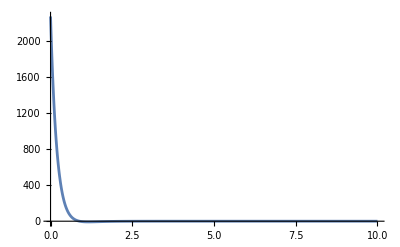

```mathematica
dAB=7.65; (*eV*)
dBC=dAB;
αAB=2.5; (*Å^-1*)
αBC=αAB;
bAB=1.162; (*Å*)
bBC=bAB;
VAB[r_] = dAB(Exp[-2αAB(r-bAB)]-2Exp[-αAB(r-bAB)]);
VBC[r_] = dBC(Exp[-2αBC(r-bBC)]-2Exp[-αBC(r-bBC)]);
Plot[VAB[r], {r, 0, 10}, PlotRange->]
```